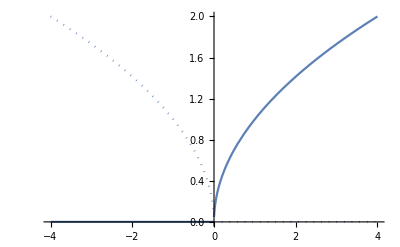

```mathematica
ReImPlot[Sqrt[x],{x,-4,4}]
```

```mathematica
D[Sin[x],{x,-2}]
```

D::dvar: Multiple derivative specifier {x,-2} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

∂_{x,-2} Sin[x]

```mathematica
D[Sin[x],{x,2}]
```

-Sin[x]

```mathematica
SurfaceData["Trinoid","Image"]
```

EntityValue::timeout: A network operation for EntityValue timed out. Please try again later.

General::stop: Further output of EntityValue::timeout will be suppressed during this calculation.

EntityValue::outdcache: Using potentially outdated cached values.

Missing[RetrievalFailure]

```mathematica
ParametricPlot3D[
{t Cos[t],t Sin[t],t}
,{t,-2,2}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{t Cos[t],t Sin[t],t},
{Cos[t],Sin[t],t}
},{t,-10,10}]
```

-Graphics3D-

```mathematica
FullSimplify[Normalize@{t Cos[t],t Sin[t],t},t∈Reals]
```

{(Cos[t] Sign[t])/(√2),(Sign[t] Sin[t])/(√2),Sign[t]/(√2)}

```mathematica
FullSimplify[Normalize@{Cos[t], Sin[t],t},t∈Reals]
```

{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))}

```mathematica
ParametricPlot3D[{
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{(Cos[t] Sign[t])/(√2),(Sign[t] Sin[t])/(√2),Sign[t]/(√2)}
},{t,-10,10}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{t Cos[t],t Sin[t],t},
{Cos[t],Sin[t],t},
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{(Cos[t] Sign[t])/(√2),(Sign[t] Sin[t])/(√2),Sign[t]/(√2)}
},{t,-30,30}]
```

-Graphics3D-

```mathematica
1
```

1

```mathematica
3
```

3

```mathematica
2
```

2

```mathematica
3
```

3

```mathematica
ParametricPlot3D[{
{t Cos[t],t Sin[t],t},
{Cos[t],Sin[t],t},
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{(Cos[t] Sign[t])/(√2),(Sign[t] Sin[t])/(√2),Sign[t]/(√2)}
},{t,-10,10}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{t Cos[t],t Sin[t],t},
{Cos[t],Sin[t],t},
{Cos[t]/(√(1+t^2)),Sin[t]/(√(1+t^2)),t/(√(1+t^2))},
{(Cos[t] Sign[t])/(√2),(Sign[t] Sin[t])/(√2),Sign[t]/(√2)}
},{t,-5,5}]
```

-Graphics3D-

```mathematica
FullSimplify[ArcCurvature[{t Cos[t],t Sin[t],t},t],t∈Reals]
```

√((8+5 t^2+t^4)/((2+t^2)^3))

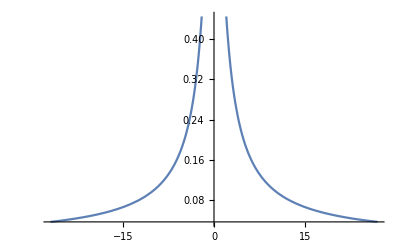

```mathematica
Plot[√((8+5 t^2+t^4)/((2+t^2)^3)),{t,-27.04,27.04}]
```

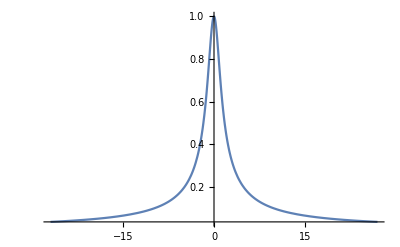

```mathematica
Plot[√((8+5 t^2+t^4)/((2+t^2)^3)),{t,-27.04,27.04},PlotRange->Full]
```

```mathematica
√((8+5 t^2+t^4)/((2+t^2)^3))==ArcCurvature[{f[t],t Sin[t],t},t]
```

√((8+5 t^2+t^4)/((2+t^2)^3))==√((4 Cos[t]^2-4 t Cos[t] Sin[t]+t^2 Sin[t]^2+4 Cos[t]^2 f'[t]^2-4 t Cos[t] Sin[t] f'[t]^2+t^2 Sin[t]^2 f'[t]^2-4 t Cos[t]^2 f'[t] f''[t]-4 Cos[t] Sin[t] f'[t] f''[t]+2 t^2 Cos[t] Sin[t] f'[t] f''[t]+2 t Sin[t]^2 f'[t] f''[t]+f''[t]^2+t^2 Cos[t]^2 f''[t]^2+2 t Cos[t] Sin[t] f''[t]^2+Sin[t]^2 f''[t]^2)/(1+t^2 Cos[t]^2+2 t Cos[t] Sin[t]+Sin[t]^2+f'[t]^2)^3)

```mathematica
FullSimplify[√((8+5 t^2+t^4)/((2+t^2)^3))==ArcCurvature[{f[t],t Sin[t],t},t],t∈Reals]
```

(8+5 t^2+t^4)/((2+t^2)^3)==((-2 Cos[t]+t Sin[t])^2 (1+f'[t]^2)+(-t-3 t Cos[2 t]+(-2+t^2) Sin[2 t]) f'[t] f''[t]+(1+(t Cos[t]+Sin[t])^2) f''[t]^2)/((1+(t Cos[t]+Sin[t])^2+f'[t]^2)^3)

```mathematica
DSolve[%22,{f[t],f[t]},{t}]
```

$Aborted

```mathematica
FullSimplify[√((8+5 t^2+t^4)/((2+t^2)^3))==ArcCurvature[{f[t]Cos[t],f[t] Sin[t],f[t]},t],t∈Reals]
```

(8+5 t^2+t^4)/((2+t^2)^3)==(f[t]^4+5 f[t]^2 f'[t]^2+8 f'[t]^4-2 f[t] (f[t]^2+4 f'[t]^2) f''[t]+2 f[t]^2 f''[t]^2)/((f[t]^2+2 f'[t]^2)^3)

```mathematica
FullSimplify[√((8+5 t^2+t^4)/((2+t^2)^3))==ArcCurvature[{f[t]Cos[f[t]],f[t] Sin[f[t]],f[t]},t],t∈Reals]
```

√((8+5 t^2+t^4)/((2+t^2)^3))==(√(8+5 f[t]^2+f[t]^4))/((2+f[t]^2)^(3/2))

```mathematica
Reduce[√((8+5 t^2+t^4)/((2+t^2)^3))==(√(8+5 f[t]^2+f[t]^4))/((2+f[t]^2)^(3/2))]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[√((8+5 t^2+t^4)/((2+t^2)^3))==(√(8+5 f[t]^2+f[t]^4))/((2+f[t]^2)^(3/2))]

```mathematica
Solve[√((8+5 t^2+t^4)/((2+t^2)^3))==(√(8+5 f[t]^2+f[t]^4))/((2+f[t]^2)^(3/2)),f[t],Reals]
```

{{f[t]→-√(t^2)},{f[t]→√(t^2)}}

```mathematica
FrenetSerretSystem[{Cos[t],Sin[t],t},t]
```

{{(√(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4))/((1+Cos[t]^2+Sin[t]^2)^(3/2)),1/(1+Cos[t]^2+Sin[t]^2)},{{-Sin[t]/(√(1+Cos[t]^2+Sin[t]^2)),Cos[t]/(√(1+Cos[t]^2+Sin[t]^2)),1/(√(1+Cos[t]^2+Sin[t]^2))},{-Cos[t]/(√(1+Cos[t]^2+Sin[t]^2) √(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4))-Cos[t]^3/(√(1+Cos[t]^2+Sin[t]^2) √(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4))-(Cos[t] Sin[t]^2)/(√(1+Cos[t]^2+Sin[t]^2) √(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4)),-Sin[t]/(√(1+Cos[t]^2+Sin[t]^2) √(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4))-(Cos[t]^2 Sin[t])/(√(1+Cos[t]^2+Sin[t]^2) √(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4))-Sin[t]^3/(√(1+Cos[t]^2+Sin[t]^2) √(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4)),0},{Sin[t]/(√(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4)),-Cos[t]/(√(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4)),(Cos[t]^2+Sin[t]^2)/(√(Cos[t]^2+Cos[t]^4+Sin[t]^2+2 Cos[t]^2 Sin[t]^2+Sin[t]^4))}}}

```mathematica
FullSimplify[FrenetSerretSystem[{Cos[t],Sin[t],t},t],t∈Reals]
```

{{1/2,1/2},{{-Sin[t]/(√2),Cos[t]/(√2),1/(√2)},{-Cos[t],-Sin[t],0},{Sin[t]/(√2),-Cos[t]/(√2),1/(√2)}}}

```mathematica
SurfaceData["Sphere","ParametricEquations"]
```

Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]]

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1][u,v]
```

{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}

```mathematica
Function[a,Function[{u,v},a {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}]][1][Cos[t],Sin[t]]
```

{Cos[Cos[t]] Sin[Sin[t]],Sin[Cos[t]] Sin[Sin[t]],Cos[Sin[t]]}

```mathematica
ParametricPlot3D[
{Cos[Cos[t]] Sin[Sin[t]],Sin[Cos[t]] Sin[Sin[t]],Cos[Sin[t]]}
,{t,-3,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{Cos[Cos[t]] Sin[Sin[t]],Sin[Cos[t]] Sin[Sin[t]],Cos[Sin[t]]}
,{t,-5,5}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{
{Cos[Cos[t]] Sin[Sin[t]],Sin[Cos[t]] Sin[Sin[t]],Cos[Sin[t]]},
{Cos[t] Sin[v],Sin[t] Sin[v],Cos[v]}
},{t,-5,5},{v,0,2π}]
```

-Graphics3D-

```mathematica
{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}/.u->t
```

{Cos[t] Sin[v],Sin[t] Sin[v],Cos[v]}

```mathematica
FullSimplify[ArcCurvature[{x,x^2},x],x∈Reals]
```

2/((1+4 x^2)^(3/2))

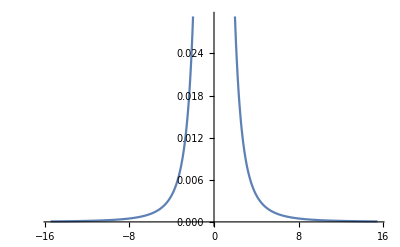

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-15.469999999999999,15.469999999999999}]
```

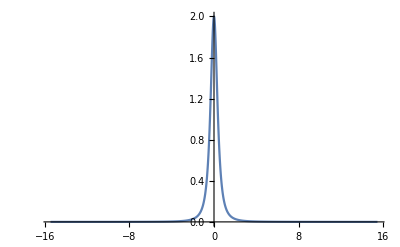

```mathematica
Plot[2/((1+4 x^2)^(3/2)),{x,-15.469999999999999,15.469999999999999},PlotRange->Full]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^4},x],x∈Reals]
```

(12 x^2)/((1+16 x^6)^(3/2))

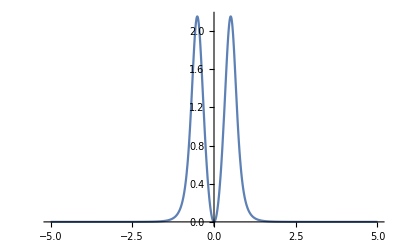

```mathematica
Plot[(12 x^2)/((1+16 x^6)^(3/2)),{x,-5,5},PlotRange->Full]
```

```mathematica
FullSimplify[ArcCurvature[{x,x^3},x],x∈Reals]
```

(6 Abs[x])/((1+9 x^4)^(3/2))

```mathematica
Plot[(12 x^2)/((1+16 x^6)^(3/2)),{x,-5,5},PlotRange->Full]
```

-Graphics-

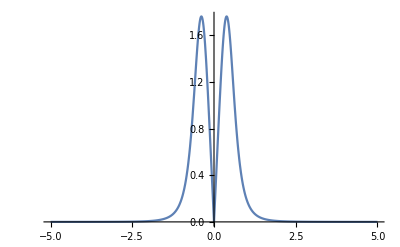

```mathematica
Plot[(6 Abs[x])/((1+9 x^4)^(3/2)),{x,-5,5},PlotRange->Full]
```

```mathematica
FullSimplify[ArcCurvature[{x,Exp[x]},x],x∈Reals]
```

ⅇ^x/((1+ⅇ^(2 x))^(3/2))

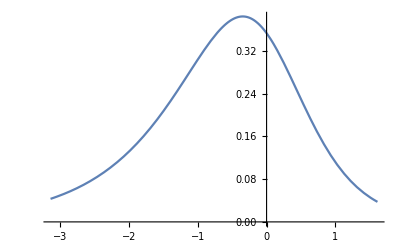

```mathematica
Plot[ⅇ^x/((1+ⅇ^(2 x))^(3/2)),{x,-3.13959465092712,1.6114359150967734}]
```

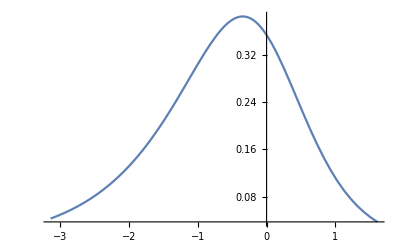

```mathematica
Plot[ⅇ^x/((1+ⅇ^(2 x))^(3/2)),{x,-3.13959465092712,1.6114359150967734},PlotRange->Full]
```

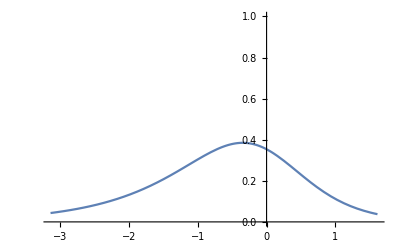

```mathematica
Plot[ⅇ^x/((1+ⅇ^(2 x))^(3/2)),{x,-3.13959465092712,1.6114359150967734},PlotRange->{0,1}]
```

```mathematica
FullSimplify[ArcCurvature[{x,Log[x]},x],x∈Reals]
```

Abs[x]/((1+x^2)^(3/2))

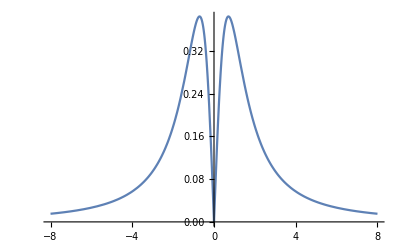

```mathematica
Plot[Abs[x]/((1+x^2)^(3/2)),{x,-8,8}]
```